```mathematica
Clear["Global`*"]
```

```mathematica
NormalizeMatrixRows[M_]:=Module[{A=M},
For[i=1,i≤Length[M],++i,
A[[i]]=Normalize[M[[i]],Total]
];
Return[A];
]
```

## Model functions

```mathematica
(*Define functions*)
g[i_,k_]:=x[i,k][t]^phi[[i]];
m[i_,k_]:=x[i,k][t]^mu[[i]];
Kf[i_]:=gamma[[i]]/(1-gamma[[i]]);
f[i_,k_]:=to[i,k]x[i,k][t]^psi[[i]](1+Kf[i])/(to[i,k]+Kf[i]);
to[i_,k_]:=(Sum[A[[i,j]]x[j,k][t],{j,S}])
lo[i_,j_,k_]:=x[i,k][t]^psi [[i]]x[j,k][t](1+Kf[i])/(Kf[i]+to[i,k])
e[i_,k_]:=-d[[i]]Sum[L[[k,l]]x[i,l][t],{l,Nvertices}]
```

## Parameterization

```mathematica
(* Local food web *)
S=3;
lima={{0,0,0},{1,0,0},{0,1,0}};

(* Spatial web *)
Nvertices=1;
L={{0}};

(*set parameters*)
For[i=1,i≤S,++i,
(*migration rate*)
d={2,3,10};

(*biomass flow*)
alpha={10,3,2};

(*exponent parameters*)
phi={1,0,0};
mu={1,1,1};
psi={0,1,1};
gamma={0,0.6,0.6};

(*scale parameters*)
sigma={0.9,0.9,0};
sigmatilde=Table[1-sigma[[i]],{i,S}];

delta={0,1,1};
deltatilde=Table[1-delta[[i]],{i,S}];

beta=Table[If[Sum[lima[[n,i]],{n,S}]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0],{j,S},{i,S}];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=2;
```

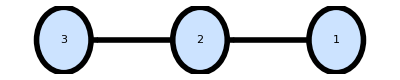

```mathematica
GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->Automatic
]
```

## Model Equations

```mathematica
(* Homogeneous system equations right hand side *)
rhs[i_,k_]:=alpha[[i]](deltatilde[[i]]g[i,k]
+delta[[i]]If[Sum[lima[[i,j]],{j,S}]>0,f[i,k],0]
-sigmatilde[[i]]m[i,k]
-sigma[[i]]Sum[beta[[j,i]]If[beta[[j,i]]>0,lo[j,i,k],0],{j,S}])
```

```mathematica
Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]]
```

{x[1,1]'[t]==10 (0.5 x[1,1][t]-(1.25 x[1,1][t] x[2,1][t])/(1.5+x[1,1][t])),x[2,1]'[t]==3 (-0.5 x[2,1][t]+(2.5 x[1,1][t] x[2,1][t])/(1.5+x[1,1][t])-(1.25 x[2,1][t] x[3,1][t])/(1.5+x[2,1][t])),x[3,1]'[t]==2 (-x[3,1][t]+(2.5 x[2,1][t] x[3,1][t])/(1.5+x[2,1][t]))}

## Bifurcation Diagram

```mathematica
CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.Table[x[i,1][t]->1,{i,S}]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];
];
```

```mathematica
phi[[1]]=ϕ;
gamma[[2]]=Subscript[γ, 2];
gamma[[3]]=Subscript[γ, 3];
CalculateJacobian[];
kappaList=N[Eigenvalues[L]];
J0//MatrixForm
JM//MatrixForm
```

(10. (-0.1+ϕ-0.9 γ_2) | -9. | 0
3 γ_2 | 2.7-2.7 γ_3 | -2.7
0 | 2 γ_3 | 0)

(2 | 0 | 0
0 | 3 | 0
0 | 0 | 10)

```mathematica
EVList=Eigenvalues[J0]
solbif=Solve[EVList==0,{Subscript[γ, 2],Subscript[γ, 3]}]
bifurcationList=Subscript[γ, 2]/.solbif;
bifurcationPlot=Plot[bifurcationList,{ϕ,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},ImageSize->1000];
parameterPicker=LocatorPane[Dynamic[{phival,gammaval}],bifurcationPlot]
Dynamic[{phi[[1]]=phival,gamma[[2]]=gammaval,gamma[[3]]=gammaval}]
```

{Root[1. #1^3+5.4 γ_3-54. ϕ γ_3+48.6 γ_2 γ_3+#1^2 (-1.7-10. ϕ+9. γ_2+2.7 γ_3)+#1 (-2.7+27. ϕ+2.7 γ_2+8.1 γ_3-27. ϕ γ_3+24.3 γ_2 γ_3)&,1],Root[1. #1^3+5.4 γ_3-54. ϕ γ_3+48.6 γ_2 γ_3+#1^2 (-1.7-10. ϕ+9. γ_2+2.7 γ_3)+#1 (-2.7+27. ϕ+2.7 γ_2+8.1 γ_3-27. ϕ γ_3+24.3 γ_2 γ_3)&,2],Root[1. #1^3+5.4 γ_3-54. ϕ γ_3+48.6 γ_2 γ_3+#1^2 (-1.7-10. ϕ+9. γ_2+2.7 γ_3)+#1 (-2.7+27. ϕ+2.7 γ_2+8.1 γ_3-27. ϕ γ_3+24.3 γ_2 γ_3)&,3]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{γ_2→1/9 (-1+10 ϕ)},{γ_3→0}}

```mathematica
NSolve[Re[EVList]==0,{ϕ,Subscript[γ, 2],Subscript[γ, 3]}]
```

NSolve[{Re[Root[1. #1^3+5.4 γ_3-54. ϕ γ_3+48.6 γ_2 γ_3+#1^2 (-1.7-10. ϕ+9. γ_2+2.7 γ_3)+#1 (-2.7+27. ϕ+2.7 γ_2+8.1 γ_3-27. ϕ γ_3+24.3 γ_2 γ_3)&,1]],Re[Root[1. #1^3+5.4 γ_3-54. ϕ γ_3+48.6 γ_2 γ_3+#1^2 (-1.7-10. ϕ+9. γ_2+2.7 γ_3)+#1 (-2.7+27. ϕ+2.7 γ_2+8.1 γ_3-27. ϕ γ_3+24.3 γ_2 γ_3)&,2]],Re[Root[1. #1^3+5.4 γ_3-54. ϕ γ_3+48.6 γ_2 γ_3+#1^2 (-1.7-10. ϕ+9. γ_2+2.7 γ_3)+#1 (-2.7+27. ϕ+2.7 γ_2+8.1 γ_3-27. ϕ γ_3+24.3 γ_2 γ_3)&,3]]}==0,{ϕ,γ_2,γ_3}]

```mathematica
CharacteristicFunction[J0]
```

CharacteristicFunction::argr: CharacteristicFunction called with 1 argument; 2 arguments are expected.

CharacteristicFunction[{{10. (-0.1+ϕ-0.9 γ_2),-9.,0},{3 γ_2,2.7-2.7 γ_3,-2.7},{0,2 γ_3,0}}]

```mathematica
Roots[CharacteristicPolynomial[J0,x]==0,x]//FullSimplify
```

$Aborted

## Homogen System

```mathematica
(*set starting conditions*)
setStartHomogen[]:=Module[{delta=0.01},
startHomogen=
Flatten[
Table[
x[i,k][0]==RandomReal[{1-delta,1+delta}],
{i,S},{k,1}]
];
];

(*Solve ODE*)
solveHomogen[Tmax_]:=Module[{sol},
setStartHomogen[];
sol=NDSolve[Join[{eqnsHomogen,startHomogen}],varsHomogen,{t,0,Tmax},MaxSteps->100000][[1]];
Return[varsHomogen/.sol];
];

EvaluateHomogenSystem[Tmax_]:=Module[{},
(*generate equations*)
eqnsHomogen=Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]];

(*dependent variables*)
varsHomogen = Flatten[
Table[
x[i,k][t]
,{i,S},{k,1}]
];

(*solve deqns*)
solHomogen=solveHomogen[Tmax];
XSList=solHomogen/.t->Tmax;

(*set steady state values*)
For[i=1,i≤S,++i,
XS[i]=XSList[[i]];
TS[i]=Sum[c[[i,j]]XS[j],{j,S}];
];
];
```

```mathematica
phival=0.1;
gammaval=0.8;
gammaval=0.8;
parameterPicker
```

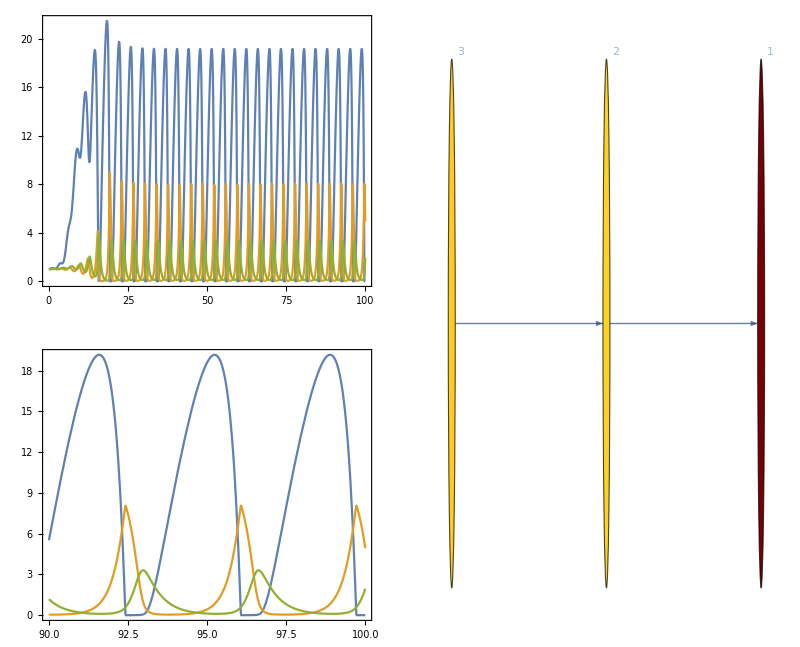

```mathematica
Tmax=100;
EvaluateHomogenSystem[Tmax];
solHomogen=solveHomogen[Tmax];

phi[[1]]=phival;
gamma[[2]]=gammaval;
gamma[[3]]=0.8;

GraphicsGrid[{
{Plot[solHomogen,{t,0,Tmax},PlotRange->Full,Frame->True],
HighlightGraph[AdjacencyGraph[c],
Table[Style[VertexList[AdjacencyGraph[c]]⟦i⟧,ColorData["SolarColors"][Rescale[solHomogen⟦i⟧/.{t->Tmax},{0,2},{0,1}]]],{i,VertexCount[AdjacencyGraph[c]]}],
VertexLabels->Table[i->i,{i,S}],
ImageSize->Large]},
{Plot[solHomogen,{t,Tmax*0.9,Tmax},PlotRange->Full,Frame->True],
SpanFromAbove}
}]
```

## Noise

```mathematica
PlotOptionsTimeSeries={PlotRange->Full,ImageSize->Small,MaxPlotPoints->1000};
```

### Local

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
Module[{y},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.1,0.1}];
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
pltLocal=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

-Graphics-

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
Module[{y},
Tmax=100;
maxsteps=100000;
dt=Tmax/maxsteps;

noise=0.01;
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.1,0.1}];
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

```mathematica
pltLocalNoise=ListLinePlot[Transpose[data],ImageSize->Small,DataRange->{0,Tmax},PlotRange->Full]
```

-Graphics-

### Spatial

```mathematica
ExportData2S6P[name_,data_]:=Module[{},
Export[name<>".CSV",Table[Join[data[[i,1]],data[[i,2]]],{i,maxsteps}]]
];
```

```mathematica
ExportData2S6P["test",data]
```

test.CSV

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
Module[{y},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.1,0.1}];
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

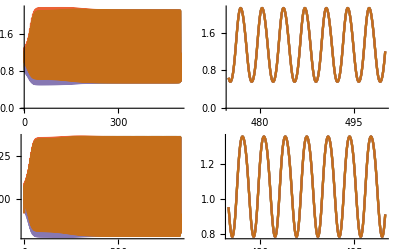

{0.99,0.525}

```mathematica
pltSpatial=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]

{phi[[1]],gamma[[2]]}
```

```mathematica
parameterStable={{0.8730000000000001,0.462},{0.8740000000000001,0.444},{0.786,0.37},{0.671,0.279},{0.9215000000000001,0.4915},{0.9455,0.5125},{0.9560000000000001,0.5205},{0.8305,0.4025},{0.7275,0.3195},{0.916,0.47100000000000003}};
parameterHomogen={{0.876,0.4045},{0.8795000000000001,0.3875},{0.915,0.444},{0.9585,0.47900000000000004},{0.994,0.5035000000000001},{1.004,0.5185},{0.8325,0.38},{0.801,0.34700000000000003},{0.796,0.354},{0.683,0.265},{0.8575,0.4005},{0.642,0.246},{0.6605000000000001,0.26},{0.6930000000000001,0.28},{0.758,0.3215},{0.7360000000000001,0.3125}};
parameterOscillation={{0.99,0.525},{0.9995,0.5385},{0.9910000000000001,0.5355},{0.9745,0.5225},{0.9625,0.5015000000000001},{0.9705,0.5135},{0.929,0.485},{0.9495,0.5045000000000001},{0.9670000000000001,0.5275}};
parameterPattern={{0.8740000000000001,0.4285},{0.8740000000000001,0.4165},{0.9725,0.5025000000000001},{0.9660000000000001,0.4915},{0.8925000000000001,0.439},{0.8545,0.40850000000000003},{0.8350000000000001,0.3915},{0.811,0.378},{0.7925000000000001,0.359},{0.6765000000000001,0.272},{0.8470000000000001,0.3985},{0.8650000000000001,0.41250000000000003},{0.8845000000000001,0.4305},{0.9390000000000001,0.47900000000000004},{0.668,0.267},{0.7025,0.2935},{0.7535000000000001,0.3285},{0.7330000000000001,0.3155},{0.9065000000000001,0.453},{0.9095000000000001,0.451},{0.9225000000000001,0.464}};
parameterDynamicPattern={{1.0030000000000001,0.5295},{0.9835,0.5145},{0.9510000000000001,0.488}};

pltParameterStable=Graphics[{PointSize->Large,RGBColor["#000000"],Point[parameterStable]}];
pltParameterHomogen=Graphics[{PointSize->Large,RGBColor["#005AA9"],Point[parameterHomogen]}];
pltParameterOscillation=Graphics[{PointSize->Large,RGBColor["#99C000"],Point[parameterOscillation]}];
pltParameterPattern=Graphics[{PointSize->Large,RGBColor["#E6001A"],Point[parameterPattern]}];
pltParameterDynamicPattern=Graphics[{PointSize->Large,RGBColor["#A60084"],Point[parameterDynamicPattern]}];

pltBifurcationDeterministic=Show[pltBifurcation,pltParameterStable,pltParameterHomogen,pltParameterOscillation,pltParameterPattern,pltParameterDynamicPattern];
LocatorPane[Dynamic[{phi[[1]],gamma[[2]]}],pltBifurcationDeterministic]
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
Simulate[noise_]:=Module[{y},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.1,0.1}];
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
];
];
```

```mathematica
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
{phi[[1]],gamma[[2]]}
```

-Graphics-

{0.99,0.525}

```mathematica
parameterList={{0.8175,0.368},{0.8165,0.375},{0.8155,0.38},{0.8165,0.383},{0.8145,0.3925}};
```

```mathematica
parameterStable={{0.6075,0.5680000000000001},{0.8740000000000001,0.462},{0.8730000000000001,0.485},{0.8715,0.5135},{0.8665,0.579}};
parameterHomogen={};
parameterOscillation={{0.994,0.5395}};
parameterPattern={};
parameterDynamicPattern={{0.9510000000000001,0.489}};

pltParameterStable=Graphics[{PointSize->Large,RGBColor["#000000"],Point[parameterList]}];
pltParameterHomogen=Graphics[{PointSize->Large,RGBColor["#005AA9"],Point[parameterHomogen]}];
pltParameterOscillation=Graphics[{PointSize->Large,RGBColor["#99C000"],Point[parameterOscillation]}];
pltParameterPattern=Graphics[{PointSize->Large,RGBColor["#E6001A"],Point[parameterPattern]}];
pltParameterDynamicPattern=Graphics[{PointSize->Large,RGBColor["#A60084"],Point[parameterDynamicPattern]}];

pltBifurcationStochastisch=Show[pltBifurcation,pltParameterStable,pltParameterHomogen,pltParameterOscillation,pltParameterPattern,pltParameterDynamicPattern];
LocatorPane[Dynamic[{phi[[1]],gamma[[2]]}],pltBifurcationStochastisch]
LocatorPane[Dynamic[{phi[[1]],gamma[[2]]}],pltBifurcationDeterministic]
```

```mathematica
{phi[[1]],gamma[[2]]}=parameterList[[3]];
Simulate[0.001];
```

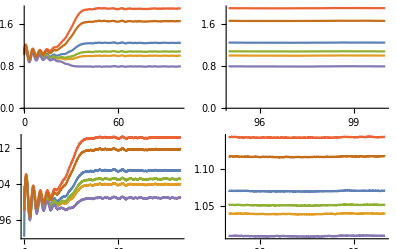

```mathematica
pltSpatialNoise=GraphicsGrid[{{
ListLinePlot[Transpose[data[[All,1]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,1]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]},
{ListLinePlot[Transpose[data[[All,2]]],Evaluate@PlotOptionsTimeSeries,DataRange->{0,Tmax}],
ListLinePlot[Transpose[Drop[data[[All,2]],0.95maxsteps]],Evaluate@PlotOptionsTimeSeries,DataRange->{0.95Tmax,Tmax}]
}}]
```

```mathematica
ExportData2S6P["data3noise0001",data]
```

data3noise0001.CSV

```mathematica
parameterList={{0.8740000000000001,0.462}};
ExportData2S6P["data2",data]
```

data1.CSV

```mathematica
Export["/home/brechtel/Dokumente/Early Warning Signs/NoiseTuring.svg",%78,"SVG"]
```

/home/brechtel/Dokumente/Early Warning Signs/NoiseTuring.svg

```mathematica
kappaList[[5]]
```

0.413094

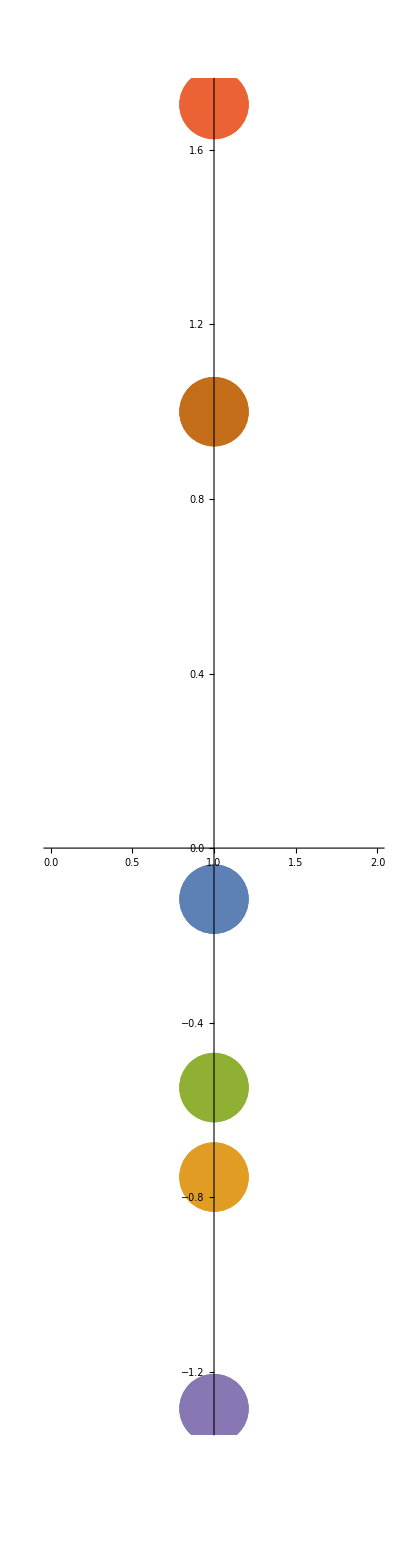

```mathematica
pltEigenvector=ListPlot[Transpose[{N[Eigenvectors[L]][[5]]}],Axes->{False,True},AspectRatio->10,PlotStyle->{PointSize->0.3},AxesOrigin->{1,0}]
```

```mathematica
Export["local.png",pltLocal]
Export["localnoise.png",pltLocalNoise]
Export["spatial.svg",pltSpatial]
Export["spatialnoise.svg",pltSpatialNoise]
Export["eigenvector.svg",pltEigenvector]
Export["bifurcation.svg",parameterPicker]
```

local.png

localnoise.png

spatial.svg

spatialnoise.svg

eigenvector.svg

bifurcation.svg

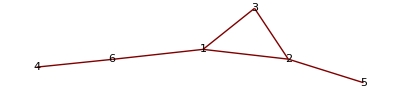

```mathematica
SpatialWeb=GraphPlot[KirchhoffGraph[L],VertexLabeling->True]
```

```mathematica
Export["spatial_web.pdf",SpatialWeb]
```

spatial_web.pdf